```mathematica
hint[tt:_String..][ll:_String..]:=Row[Riffle[{tt},Tooltip[Mouseover["💡","💡"],Style[#,12,"Text"]]&/@{ll}],BaseStyle->"Text"];
hintE[tt:_String..][ll:_String..]:=Row[Riffle[{tt},Tooltip[Mouseover[" =^💡 "," =^💡 "],Style[#,12,"Text"]]&/@{ll}],BaseStyle->"Text"];
```

## Ley de Gauss en problemas con simetría esférica o cilíndrica

Ley de Gauss en forma diferencial:	∇·E⃗ = ρ/ϵ_0.
Ley de Gauss en forma integral:	∯_S  E⃗ · OverVector[ⅆS] = Q/ϵ_0; Q es la carga total en el volumen cerrado por S.

Denominamos con Φ el flujo “cerrado” ∯_S  E⃗ · OverVector[ⅆS], con lo cual la ley de Gauss se describe así:

Φ=Q/ϵ_0

La ley de Gauss simplifica la solución de problemas donde la distribución de la carga eléctrica tiene simetría esférica o cilíndrica. Así son los problemas desde 2.6 a 2.11. En ambos casos de simetría la densidad de la carga ρ depende solo de la coordinada radial r, donde r tiene diferentes expresiones según la simetría:

a) Simetría esférica:     ρ(x,y,z)=ρ(r), donde r=√(x^2+y^2+z^2);
b) Simetría cilíndrica: ρ(x,y,z)=ρ(r), donde r=√(x^2+y^2).

En la siguiente figura dinámica se pueden visualizar las tres distribuciones r^2,ⅇ^-r y sin^2(2π r) presentadas en las dos simetrías.

```mathematica
Row[{Manipulate[SliceDensityPlot3D[f[x,y,z],{"CenterCutSphere",π/2},{x,y,z}∈Ball[],PlotLegends->Automatic,AxesStyle->{Red,Green,Blue},AxesLabel->{"X","Y","Z"},ImagePadding->15,PlotLabel->"Simetría esférica: ρ(x,y,z) = ρ(r)\ndonde r=√(x^2+y^2+z^2)"],{{f,Sin[2π √(#^2+#2^2+#3^2)]^2&,Style["Selección de función de densidad ρ(r) = ",10]},{(#^2+#2^2+#3^2)&->"r^2",ⅇ^(-√(#^2+#2^2+#3^2))&-> "ⅇ^-r",Sin[2π √(#^2+#2^2+#3^2)]^2&->"sin^2(2π r)"},ControlType->PopupMenu},Paneled->False,ControlPlacement->Top],
Manipulate[SliceDensityPlot3D[f[x,y],{x==0,y==0,z==zz,x^2+y^2==1},{x,-1,1},{y,-1,1},{z,-1,1},AxesStyle->{Red,Green,Blue},AxesLabel->{"X","Y","Z"},ImagePadding->15,PlotLabel->"Simetría cilíndrica: ρ(x,y,z) = ρ(r)\ndonde r=√(x^2+y^2)"],{{f,Sin[2π √(#^2+#2^2)]^2&,Style["Selección de función de densidad ρ(r) = ",10]},{(#^2+#2^2)&-> "r^2",ⅇ^(-√(#^2+#2^2))&-> "ⅇ^-r",Sin[2π √(#^2+#2^2)]^2&->"sin^2(2π r)"},ControlType->PopupMenu},{{zz,0,Style["Posicionar el plano perpendicular al eje Z",10]},-1,1,Appearance->"Labeled",ImageSize->Tiny},Paneled->False,ControlPlacement->Top]}]
```

Las superfícies de Gauss son cerradas y dependen de la simetría:
a) En caso de simetría esférica son esféras vacías con radio r centradas en el origen del sistema de coordenadas;
b) En el caso de simetría cilíndrica son presentadas con un tubo coaxial al eje Z y radio r cerradas con dos planos perpendiculares al eje Z.

La ley de Gauss permite calcular el componente radial E=E_r del campo eléctrico E⃗ en función de la carga Q dentro la sureficie de Gauss S. Sabiendo el componente radial nos permite expresar, y este es la aplicación principal de la ley de Gauss, el campo vectorial eléctrico E⃗ y el campo escalar potencial ϕ con las siguientes fórmulas que son válidas para ambos simetrías:

E⃗=E  OverVector[e_r]
ϕ=-∫Eⅆr.

#### (opcional) Prueba de las acuaciones (3)

Expresamos la densidad de la carga eléctrica ρ(x,y,z) con la única coordinada r según las ecuaciones (2), ρ(x,y,z)⇒ρ(r). El potencial eléctrico ϕ se deduce mediante la densidad ρ(r) y por lo tanto dependerá únicamente de la coordenada r: ϕ(x,y,z)⇒ϕ(r). Calculamos E⃗ en coordenadas esféricas y cilíndricas:

(E⃗)_esféricas=(E_r,E_θ,E_φ)=-∇ϕ=-∂_r ϕ(r) OverVector[e_r]-1/r∂_θ ϕ(r) OverVector[e_θ]-1/(r sin θ)∂_φ ϕ(r) OverVector[e_φ]=-∂_r ϕ(r) OverVector[e_r]=-∂_r ϕ(r) OverVector[e_r]=E OverVector[e_r];
(E⃗)_cilindricas=(E_r,E_φ,E_z)=-∇ϕ=-∂_r ϕ(r) OverVector[e_r]-1/r∂_φ ϕ(r) OverVector[e_φ]-∂_z ϕ(r) OverVector[e_z]=-∂_r ϕ(r) OverVector[e_r]=-∂_r ϕ(r) OverVector[e_r]=EOverVector[e_r].

Para ambos simetrías hemos recibido la misma expresión del campo vectorial eléctrico E⃗=E OverVector[e_r], donde

E=E_r=-∂/(∂r)ϕ(r),

y por lo tanto

ϕ=-∫Eⅆr.

## Algoritmo en 4 pasos para los problemas con la ley de Gauss

Los problemas de 2.6 a 2.11 tienen simetría esférica o cilíndrica. Para estos problemas conviene usar el teorema de Gauss para calcular el campo eléctrico E⃗ sabiendo la distribución de carga  ρ(r).

### Paso 1. Dibujar la superficie S de Gauss

Como ejemplos en la figura abajo están presentadas en rojo las superficies de Gauss correspondientes de los problemas 2.6 y 2.7 con simetrías cilíndrica y esférica, correspondiente.

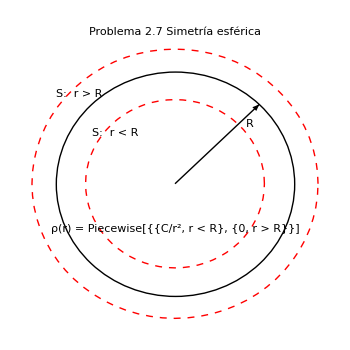
-Graphics-     -Graphics-

```mathematica
Row[{Show[-Graphics-,PlotLabel-> " Problema 2.6\nSimetría cilíndrica",ImageSize->350],"     ",Graphics[{Thick,Circle[],Arrow@{{0,0},{1,1}/√2},Dashed,Thin,Red,Circle[{0,0},1.2],Circle[{0,0},.75],Black,Text[Style["R","Text"],{.63,.53}],Text["S:  r < R",{-.5,.45},Automatic,{1,1}],Text["S:  r > R",{-.8,.8},Automatic,{1,1}],Text[Style["ρ(r) = Piecewise[{{C/r^2, r < R}, {0, r > R}}]",Larger],{0,-.4}]},PlotLabel-> " Problema 2.7\nSimetría esférica",ImageSize->350]}]
```

### Paso 2. Calcular el flujo Φ

Caso de simetría esférica; S es una esfera con radio r.

```mathematica
hintE["TraditionalForm`Φ","∯","∯","TraditionalForm`","TraditionalForm`E","TraditionalForm`E"]["Por definición","E \nOverVector[ⅆS] = n⃗ ⅆS, n⃗ = OverVector[e_r] = (1,0,0) ⟹ OverVector[ⅆS] = (ⅆS,0,0) ","TraditionalForm`(E, 0, 0)·(ⅆS, 0, 0)\  = \ E\ ⅆS\ ","TraditionalForm`E = E(r) = const\ sobre\ la\ superfície\ S","∯_S  ⅆS por definición es la area de la superfície S"]
```

TraditionalForm`Φ∯∯TraditionalForm`TraditionalForm`ETraditionalForm`E

Caso de simetría cilíndrica; S es un tubo con radio r y longitud L, que esta cerrado con dos discos (tapas) con radio r.

```mathematica
hintE["TraditionalForm`Φ = ∯","∫∫","∫∫","TraditionalForm`","TraditionalForm`E","TraditionalForm`E\ L\ 2  π\ r"]["El flujo a través de una superfície S es suma\nde los flujos a través de las partes de S","El flujo a través de las tapas es cero porque las normalas de\nlas tapas (n⃗)_(arriba  \n  abajo) = (0,0,±1) son perpendiculares de E⃗","TraditionalForm` TraditionalForm`E\ ⅆS porque E⃗ y OverVector[ⅆS] son paralelos",
"E = E(r)= const sobre el tubo","(∫∫)_S_tuboⅆS por definición es la area del tubo L 2 π r"]
```

TraditionalForm`Φ = ∯∫∫∫∫TraditionalForm`TraditionalForm`ETraditionalForm`E\ L\ 2  π\ r

#### (Opcional) Sustituir Φ en la ley de Gauss (1) y expressar el componente E

Simétria esférica: 	E=Q/(4π ϵ_0 r^2)
Simetría cilíndrica:            E=Q/(2π ϵ_0 r L)

### Paso 3. Calcular la carga Q

Para encontrar la componente radial E tenemos que calcular la carga Q en el volumen V cerrado por S, usando la densidad volúmica ρ(r).

Caso de simetría esférica

```mathematica
hintE["TraditionalForm`Q","TraditionalForm`","TraditionalForm`","TraditionalForm`","TraditionalForm`4"]["Por definición","En coordenadas esféricas ⅆV = r^2sin(θ) ⅆr ⅆθ ⅆφ","TraditionalForm`Factorizar\ en\ integral\ triple","(∫^π)_(θ = 0)sin(θ)ⅆθ = 2\n(∫^(2  π))_(φ = 0) ⅆφ = 2 π"]
```

TraditionalForm`QTraditionalForm`TraditionalForm`TraditionalForm`TraditionalForm`4

Caso de simetría cilíndrica

```mathematica
hintE["TraditionalForm`Q = TraditionalForm`","TraditionalForm`","∫_0 ","TraditionalForm`2"]["En coordenadas cilíndricas ⅆV = r ⅆr ⅆφ ⅆz","TraditionalForm`Factorizar\ en\ integral\ triple","(∫^(L/2))_(z = -L/2)ⅆz = L\n(∫^(2  π))_(φ = 0) ⅆφ = 2 π"]
```

TraditionalForm`Q = TraditionalForm`TraditionalForm`∫_0 TraditionalForm`2

#### (Opcional) Sustituir Q en la expressión de E

Simétria esférica: 	E=1/(ϵ_0 r^2)(∫_0)^r ρ(r)r^2 ⅆr
Simetría cilíndrica:            E=1/(ϵ_0 r)(∫_0)^r ρ(r)rⅆr

### Paso 4. Presentar el campo eléctrico vectorial E⃗ y calcular su potencial escalar ϕ

Sabiendo la simetría y el componente radial E, fórmula (5), presentamos el campo vectorial eléctrico segun la ecuación (3): E⃗=E OverVector[e_r].

Y otra vez usando la ecuación (3) calculamos el potencial ϕ(r) como integral indefinido, teniendo en cuenta el cumplimiento de la condición de contorno ϕ(∞)=0.

## Demonstraciones del algoritmo con varios problemas

### Problema 2.9

Un cilindre no conductor infinitament larg de radi R presenta una densidad de càrrega volúmica ρ(r). Calculeu la càrrega per unitat de longitud del cilindre i el camp elèctric a qualsevol punt de l’espai (r<R i r>R) en el casos següents:
a) ρ(r)=a r;
b) ρ(r)=C r^2.

#### Solución

Paso 1. Dibujar la superfície de Gauss:

Paso 2. Calcular el flujo Φ. Repetimos las ecuaciones (6).

Φ=∯_S E⃗·OverVector[ⅆS]=(∫∫)_S_tapa_arriba+(∫∫)_S_tapa_abajo+(∫∫)_S_tubo=(∫∫)_S_tubo E⃗·OverVector[ⅆS]=(∫∫)_S_tubo E ⅆS=E(∫∫)_S_tubo ⅆS=E 2π r L

Paso 3. Calcular la carga Q. Repetimos las ecuaciones (8),

Q=∫∫_V ∫ ρ(r)ⅆV=∫∫_V ∫ ρ(r)  r ⅆrⅆφⅆz=(∫_0)^r ρ(r) rⅆr (∫_0)^(2π)ⅆφ (∫_(-L/2))^(L/2)ⅆz=2π L(∫_0)^r ρ(r)rⅆr

y en el último ecuación cambiamos ρ(r) con C r^2:

Q=2π L(∫_0)^r C r^2 rⅆr=2π L C(∫_0)^r r^3 ⅆr=(π L C)/2 Piecewise[{{r^4, r<R}, {R^4, r>R}}]

Paso 4. Calcular el campo E⃗

E 2π r L=(π L C)/(2 ϵ_0)Piecewise[{{r^4, r<R}, {R^4, r>R}}]

E=C/(4 ϵ_0)Piecewise[{{r^3, r<R}, {R^4/r, r>R}}]

E⃗=E OverVector[e_r]

### Problema 2.11a

#### Solución

Encontrar el potencial para una distribución esférica con densidad ρ(r)=Piecewise[{{K r^2, r<R}, {0, r>R}}]

Paso 1 (Dibujar la superficie S de Gauss)

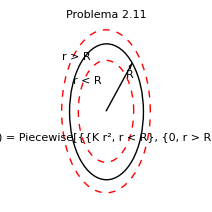

```mathematica
Graphics[{Thick,Circle[],Arrow[{{0,0},{1,1}/√2}],Dashed,Thin,Red,Circle[{0,0},1.2],Circle[{0,0},.75],Black,Text[Style["R","Text"],{.63,.53}],Text["r < R",{-.5,.45},Automatic,{1,1}],Text["r > R",{-.8,.8},Automatic,{1,1}],Text[Style["ρ(r) = Piecewise[{{K r^2, r < R}, {0, r > R}}]",Larger],{0,-.4}]},ImageSize->300,PlotLabel-> "Problema 2.11"]
```

Paso 2 (Calcular el flujo Φ(r) que atraviesa S con radio r)

Φ(r)=∯_S E⃗·OverVector[ⅆS]=∯_S (E,0,0)·(ⅆS,0,0)=∯_S EⅆS=E∯_S ⅆS=E 4π r^2

Paso 3 (Calcular la carga Q dentro de S con radio r)

Q(r)=∫∫_V ∫ ρ(r)ⅆV=∫∫_V ∫ ρ(r)  r^2 sin(θ)ⅆrⅆθⅆφ=(∫_0)^r ρ(r) r^2 ⅆr(∫_0)^π sin(θ)ⅆθ (∫_0)^(2π)ⅆφ=4π(∫_0)^r ρ(r)r^2 ⅆr

Calcular la integral en el último término usando ρ(r)=Piecewise[{{K r^2, r<R}, {0, r>R}}]. Para r<R tenemos

(I_(r<R)=(∫_0)^r ρ(r)  r^2 ⅆr=K(∫_0)^r  r^4 ⅆr=K (r^5/5)|)_(r=0)^(r=r)=K/5 r^5,

y para r>R tenemos

I_(r>R)=K/5 R^5.

Por lo tanto para la carga Q dentro de la esfera de Gauss con radio r tenemos

Q(r)=(4π K)/5 Piecewise[{{r^5, r<R}, {R^5, r>R}}].

Paso 4 (Calcular el campo eléctrico E⃗ y su potencial ϕ)

Utilizando la ley de Gauss Φ=Q/ϵ_0 y las expresiones para Φ y Q de arriba tenemos

E 4π r^2=(4π K)/(5 ϵ_0)Piecewise[{{r^5, r<R}, {R^5, r>R}}]

y despejando E

E=K/(5 ϵ_0)Piecewise[{{r^3, r<R}, {R^5/r^2, r>R}}]

El potencial ϕ mediante la formula (4):

ϕ=-∫E(r)ⅆr=-K/(5 ϵ_0)Piecewise[{{∫r^3 ⅆr, r<R}, {R^5∫ⅆr/r^2, r>R}}]=-K/(5 ϵ_0)Piecewise[{{r^4/4+C_1, r<R}, {R^5(-1/r+C_2), r>R}}]

Cuando r→∞ el potencial debe cumplir ϕ(r)→0, así que C_2=0. Para encontrar C_2 utilizamos que el potencial es una función continua, así que cuando r→R tenemos

r^4/4+C_1=^(r→R)R^5(-1/r+C_2) ⟹ R^4/4+C_1=-R^4 ⟹ C_1=-(5 R^4)/4

En final

ϕ =-K/(5 ϵ_0)Piecewise[{{r^4/4-(5 R^4)/4, r<R}, {-R^5/r, r>R}}]=(K R^4)/(20 ϵ_0)Piecewise[{{5-(r/R)^4, r<R}, {4 R/r, r>R}}]